```mathematica
En[kx_,ky_]:= -2 ( Cos[kx] + Cos[ky]);
```

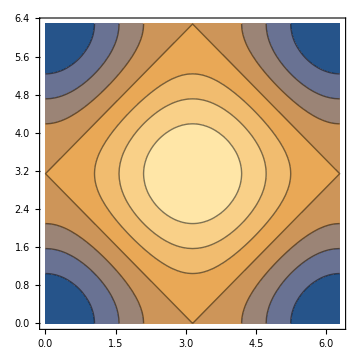

```mathematica
ContourPlot[ En[kx,ky],{kx,0,2π},{ky,0,2π}]
```

```mathematica
b1= 2π{1,0}; b2 = 2π{0,1};
```

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0.0,1.0,1.0/krange},{j,0.0,1.0,1.0/krange}],1]];
```

```mathematica
Chi[qx_,qy_,μ_]:= 1/Length[ kSpan[25]] Sum[ 1/(En[ k[[1]]+qx,k[[2]]+qy]-   En[ k[[1]],k[[2]]])(Fermi[ 10, En[ k[[1]]+qx,k[[2]]+qy]-μ]-Fermi[ 10, En[ k[[1]],k[[2]]]-μ]), {k,kSpan[25]}];
```

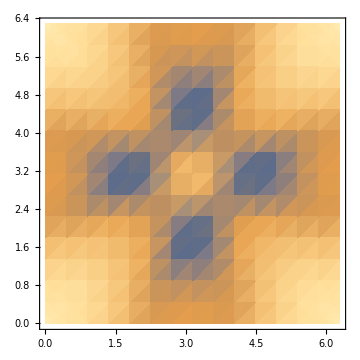

```mathematica
DensityPlot[ Chi[qx,qy,1],{qx,0,2π},{qy,0,2π}]
```

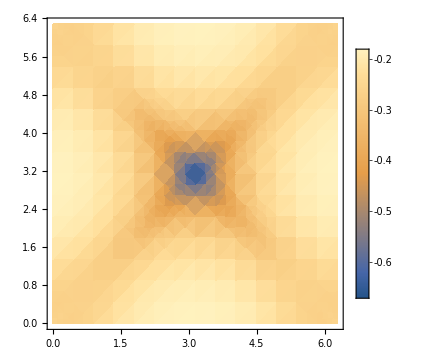

```mathematica
DensityPlot[ Chi[qx,qy,0],{qx,0,2π},{qy,0,2π},PlotRange->All,PlotLegends->Automatic]
```